### y GW AdS-S

#### GW soln

```mathematica
met5D = l^2/z^2{{-g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
Simplify[met5D /.g[z]->1-z^4/zh^4/.z->l^2/ρ]//MatrixForm
```

(l^6/(zh^4 ρ^2)-ρ^2/l^2 | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | ρ^2/(l^2 (1-l^8/(zh^4 ρ^4))) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

```mathematica
Solve[y^2-y-m^2/16==0,y]
```

{{y→1/4 (2-√(4+m^2))},{y→1/4 (2+√(4+m^2))}}

So this exactly matches Criminelli and Rattazi, except for the second solution

Try going to the special coordinate they define:

```mathematica
Simplify[ϕeqn/.ρ->ρh y^(1/4)]
```

ρh (-l^2 m^2 y^(3/4) ϕ[y^(1/4) ρh]+ρh ((-1+5 y) ϕ'[y^(1/4) ρh]+(-1+y) y^(1/4) ρh ϕ''[y^(1/4) ρh]))==0

need to do it from the metric instead.

```mathematica
met5D = l^2/z^2{{g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4),θ,ϕ};
x= {t,r,y,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ];
gy //MatrixForm 
Simplify[Det[gy]]

g5y = Det[gy];
ϕeqn =Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[3,3]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[y],y];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[y]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos2=ϕ[y]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

{{(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((ρ^4-ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

(r^4 ρ^6 Sin[θ]^2)/l^6

(((-1+y) ρh^2)/(l^2 √y) | 0 | 0 | 0 | 0
0 | (√y ρh^2)/l^2 | 0 | 0 | 0
0 | 0 | l^2/(16 (-1+y) y) | 0 | 0
0 | 0 | 0 | (r^2 √y ρh^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 √y ρh^2 Sin[θ]^2)/l^2)

(r^4 ρh^8 Sin[θ]^2)/(16 l^6)

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])==0

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

```mathematica
Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[3,3]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]
```

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])

```mathematica
(1-z^4/zh^4)
Simplify[(1-fz)^-1-1]
```

1-z^4/zh^4

fz/(1-fz)

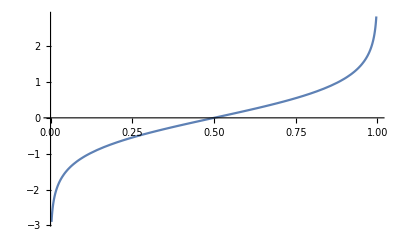

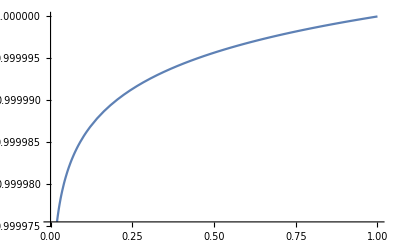

```mathematica
Plot[ϕos2/.m->0.01/l,{y,0,1}]
Plot[ϕos1/.m->0.01/l,{y,0,1}]
```

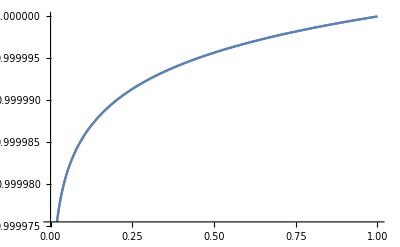

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,0,1}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y]/.m->0.01/l,{y,0,1}] }]
```

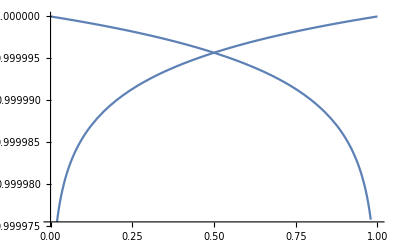

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,0,1}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y]/.m->0.01/l,{y,0,1}] }]
```

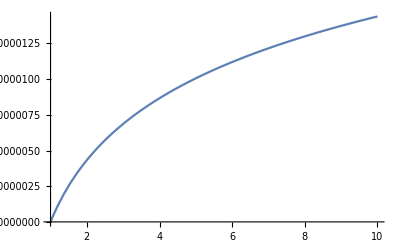

```mathematica
Show[{Plot[ϕos1/.m->0.01/l,{y,1,10}], Plot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y]/.m->0.01/l,{y,1,10}] }]
```

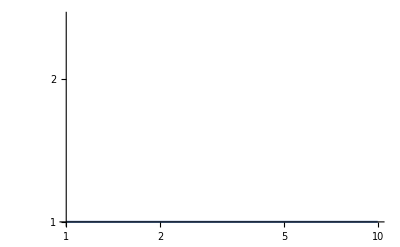

```mathematica
Show[{LogLogPlot[ϕos2/.m->0.01/l,{y,1,10}], LogLogPlot[Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y]/.m->0.01/l,{y,1,10}] }]
```

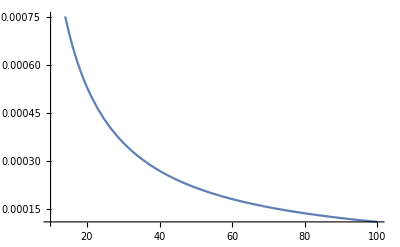

```mathematica
ϕCR[ρ_,ϵ_]:=(ρ^ϵ-ϵ/8 ρ^(-4+ϵ)+ϵ/8 ρ^(-4-ϵ))
Plot[ϕCR[ρ,0.01]D[ϕCR[ρ,0.01],ρ]/.ρ->a,{a,10,100}]
```

This shows that the solution we got in Mathematica matches CR - to be more explicit: so at least the second works.

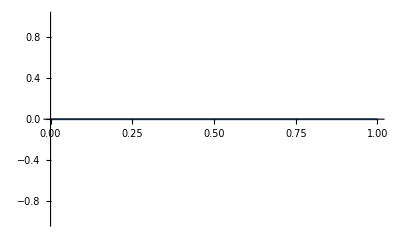

```mathematica
Show[{Plot[(ϕos1 -Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,1-y])/.m->0.01/l,{y,0,1}] }]
```

It looks like the other solution they give is just a flipped version of the same thing.

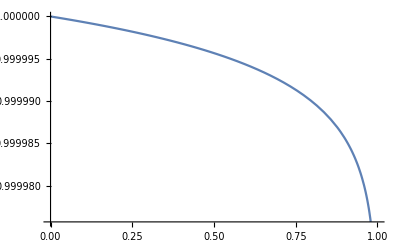

```mathematica
Plot[(Hypergeometric2F1[1/2-1/4 √(4+l^2 m^2),1/2+1/4 √(4+l^2 m^2),1,y])/.m->0.01/l,{y,0,1}]
```

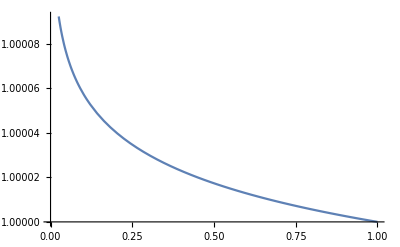

```mathematica
Plot[ϕos1/.{m->0.01/l,y->ρ^4}/.ρ->1/z,{z,0,1}]
```

#### Solution in terms of y and handling branch cut

```mathematica
ϕos1type3 = PowerExpand[Simplify[LegendreP[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]
ϕos2type3 =PowerExpand[Simplify[LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]
```

LegendreP[ϵ/4,-1+2 y]

LegendreQ[ϵ/4,0,3,-1+2 y]

```mathematica
FullSimplify[D[ϕos1type3,y]]
D[LegendreP[ϵ/4,y],y]
D[Hypergeometric2F1[a,b,1,z],z]
```

((4+ϵ) (LegendreP[1+ϵ/4,-1+2 y]+(1-2 y) LegendreP[ϵ/4,-1+2 y]))/(8 (-1+y) y)

((1+ϵ/4) LegendreP[1+ϵ/4,y]+y (-1-ϵ/4) LegendreP[ϵ/4,y])/(-1+y^2)

a b Hypergeometric2F1[1+a,1+b,2,z]

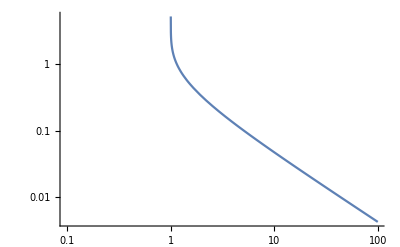

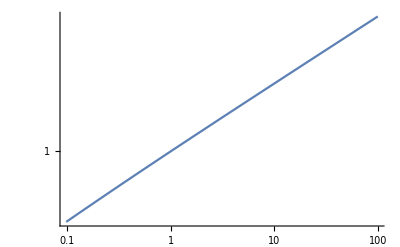

```mathematica
LogLogPlot[ϕos2type3/.ϵ->0.1,{y,0,100}]
LogLogPlot[ϕos1type3/.ϵ->0.1,{y,0,100}]
```

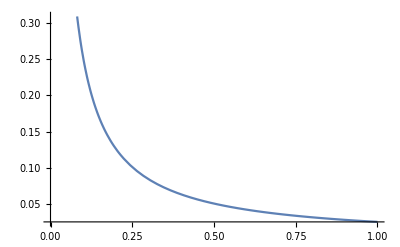

```mathematica
Plot[D[ϕos1type3/.ϵ->0.1,y]/.y->yt,{yt,1,10^-4}]
```

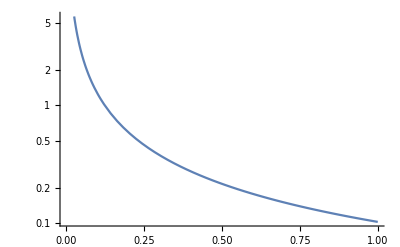

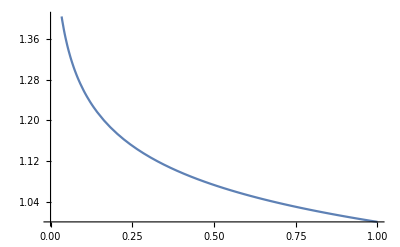

```mathematica
LogPlot[Abs[D[ϕos1type3/.ϵ->0.1/.y->1/z^4,z]/.z->zt],{zt,1,10^-10}]
Plot[ϕos1type3/.ϵ->0.1/.y->1/z^4,{z,1,10^-6}]
```

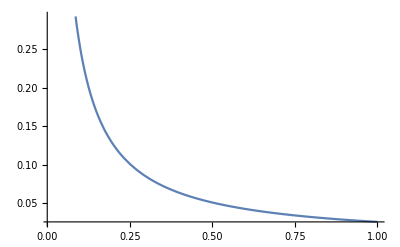

```mathematica
Plot[D[ϕos1type3/.ϵ->0.1,y]/.y->yt,{yt,1,10^-2}]
```

This means that away from the horizon the scalar barely changes with the motion of the wall. How do we quantify this?

```mathematica
ϕos1type3
```

LegendreP[ϵ/4,-1+2 y]

```mathematica
FullSimplify[Series[ϕos1type3,{y,∞,1}]]
FullSimplify[Series[ϕos1type3/.y->zh^4/z^4,{z,0,4}]]
```

(-1+y)^(-ϵ/4) ((-1+y)^(ϵ/2) (Gamma[1+ϵ/2]/Gamma[1+ϵ/4]^2+(ϵ Gamma[1+ϵ/2])/(8 Gamma[1+ϵ/4]^2 y)+O[1/y]^2)+(Gamma[-1-ϵ/2]/(Gamma[-ϵ/4]^2 y)-((-4+ϵ) Gamma[-1-ϵ/2])/(8 Gamma[-ϵ/4]^2 y^2)+O[1/y]^3))

(zh^4/z^4)^(-ϵ/4) (((Gamma[-1-ϵ/2] z^4)/(zh^4 Gamma[-ϵ/4]^2)+O[z]^5)+(zh^4/z^4)^(ϵ/2) (Gamma[1+ϵ/2]/Gamma[1+ϵ/4]^2-((ϵ Gamma[1+ϵ/2]) z^4)/(8 (zh^4 Gamma[1+ϵ/4]^2))+O[z]^5))

```mathematica
Series[Gamma[1+ϵ/2]/Gamma[1+ϵ/4],{ϵ,0,1}]
```

1-(EulerGamma ϵ)/4+O[ϵ]^2

```mathematica
FullSimplify[Series[ϕos1type3/.y->zh^4/z^4,{z,zh,4}]]
```

1-((ϵ (4+ϵ)) (z-zh))/(4 zh)+(ϵ (4+ϵ) (8+ϵ (4+ϵ)) (z-zh)^2)/(64 zh^2)-((ϵ (2+ϵ)^2 (4+ϵ) (48+ϵ (4+ϵ))) (z-zh)^3)/(2304 zh^3)+1/(147456 zh^4)ϵ (4+ϵ) (24+ϵ (4+ϵ)) (384+ϵ (4+ϵ) (136+ϵ (4+ϵ))) (z-zh)^4+O[z-zh]^5

#### Total phi near probe

```mathematica
Clear[ϕ]
(*ϕb[y_]:=HeavisideTheta[y0-y] (Ab ϕos1type3)
ϕa[y_]:= HeavisideTheta[y-y0] (Aa ϕos1type3+ Ba ϕos2type3)*)
ϕb[y_]:= (Ab ϕos1type3)
ϕa[y_]:=(Aa ϕos1type3+ Ba ϕos2type3)
ϕtotal[y_]:= HeavisideTheta[y0-y] (Ab ϕos1type3) + HeavisideTheta[y-y0] (Aa ϕos1type3+ Ba ϕos2type3) 
ϕtotal1[y_]:= HeavisideTheta[y0-y] (Ab D[ϕos1type3,y]) + HeavisideTheta[y-y0] (Aa D[ϕos1type3,y]+ Ba D[ϕos2type3,y]) 
ϕtotal2[y_]:= HeavisideTheta[y0-y] (Ab D[ϕos1type3,{y,2}]) + HeavisideTheta[y-y0] (Aa D[ϕos1type3,{y,2}]+ Ba D[ϕos2type3,{y,2}]) 
ϕtotald[y_,d_]:= HeavisideTheta[y0-y] (Ab D[ϕos1type3,{y,d}]) + HeavisideTheta[y-y0] (Aa D[ϕos1type3,{y,d}]+ Ba D[ϕos2type3,{y,d}])
```

```mathematica
D[ϕtotal[y],{y,2}]
```

-(4 Ab DiracDelta[-y+y0] ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+4 Ab HeavisideTheta[-y+y0] (-((-1+2 y) (4+ϵ) LegendreP[1+ϵ/4,-1+2 y])/(2 (-1+(-1+2 y)^2)^2)+((32 (-1+2 y)^2-4 ϵ+12 (-1+2 y)^2 ϵ-ϵ^2+(-1+2 y)^2 ϵ^2) LegendreP[ϵ/4,-1+2 y])/(16 (-1+(-1+2 y)^2)^2))+2 DiracDelta[y-y0] ((2 Aa ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+(2 Ba ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))+HeavisideTheta[y-y0] (4 Aa (-((-1+2 y) (4+ϵ) LegendreP[1+ϵ/4,-1+2 y])/(2 (-1+(-1+2 y)^2)^2)+((32 (-1+2 y)^2-4 ϵ+12 (-1+2 y)^2 ϵ-ϵ^2+(-1+2 y)^2 ϵ^2) LegendreP[ϵ/4,-1+2 y])/(16 (-1+(-1+2 y)^2)^2))+Ba (-(8 (-1+2 y) ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/((-1+(-1+2 y)^2)^2)+1/(-1+(-1+2 y)^2)2 ((2 (1+ϵ/4) ((-1+2 y) (-2-ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(2+ϵ/4) LegendreQ[2+ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2)+2 (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]+(2 (-1+2 y) (-1-ϵ/4) ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))))+(Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y]) DiracDelta'[y-y0]+Ab LegendreP[ϵ/4,-1+2 y] DiracDelta'[-y+y0]

```mathematica
ϕtotald[y,1]
```

(2 Ab HeavisideTheta[-y+y0] ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+HeavisideTheta[y-y0] ((2 Aa ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+(2 Ba ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))

```mathematica
ϕtotal1[y]
```

(2 Ab HeavisideTheta[-y+y0] ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+HeavisideTheta[y-y0] ((2 Aa ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+(2 Ba ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))

```mathematica
ϕtotal[y]
ϕtotal2[y]
ϕtotal1[y]
```

Ab HeavisideTheta[-y+y0] LegendreP[ϵ/4,-1+2 y]+HeavisideTheta[y-y0] (Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y])

4 Ab HeavisideTheta[-y+y0] (-((-1+2 y) (4+ϵ) LegendreP[1+ϵ/4,-1+2 y])/(2 (-1+(-1+2 y)^2)^2)+((32 (-1+2 y)^2-4 ϵ+12 (-1+2 y)^2 ϵ-ϵ^2+(-1+2 y)^2 ϵ^2) LegendreP[ϵ/4,-1+2 y])/(16 (-1+(-1+2 y)^2)^2))+HeavisideTheta[y-y0] (4 Aa (-((-1+2 y) (4+ϵ) LegendreP[1+ϵ/4,-1+2 y])/(2 (-1+(-1+2 y)^2)^2)+((32 (-1+2 y)^2-4 ϵ+12 (-1+2 y)^2 ϵ-ϵ^2+(-1+2 y)^2 ϵ^2) LegendreP[ϵ/4,-1+2 y])/(16 (-1+(-1+2 y)^2)^2))+Ba (-(8 (-1+2 y) ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/((-1+(-1+2 y)^2)^2)+1/(-1+(-1+2 y)^2)2 ((2 (1+ϵ/4) ((-1+2 y) (-2-ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(2+ϵ/4) LegendreQ[2+ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2)+2 (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]+(2 (-1+2 y) (-1-ϵ/4) ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))))

(2 Ab HeavisideTheta[-y+y0] ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+HeavisideTheta[y-y0] ((2 Aa ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)+(2 Ba ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2))

{y0→2,ϵ→0.1,Ab→1,Aa→1,Ba→1}

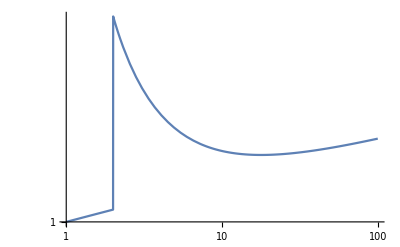

```mathematica
Replacement = {y0->2,ϵ->0.1,Ab->1,Aa->1,Ba->1}
LogLogPlot[ϕtotal[y]/.Replacement,{y,1,100},PlotRange->All]
```

Sub back into eom

```mathematica
met5D = l^2/z^2{{g[z],0,0,0,0},{0,1,0,0,0},{0,0,1/g[z],0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}}
X= {t,r,l^2/ρ,θ,ϕ};
x= {t,r,ρ,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gρ = Simplify[Transpose[JXx].(met5D/.g[z]->1-z^4/zh^4/.z->l^2/ρ/.zh->l^2/ρh).JXx ];
gρ //MatrixForm 
Simplify[Det[gρ]]

X= {t,r,ρh y^(1/4),θ,ϕ};
x= {t,r,y,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gy = Simplify[Transpose[JXx].(gρ/.ρ->ρh y^(1/4)).JXx ];
gy //MatrixForm 
Simplify[Det[gy]]

g5y = Det[gy];
ϕeqn =Simplify[-(1/(√g5y)D[√g5y Inverse[gy][[3,3]]D[ϕ[y],y],y]-m^2 ϕ[y])l^2]==0
(*Simplify[ϕeqn/.ρ->y/ρh/.ϕ[ρh-ρ]->ϕ[ρ]]*)
ϕsol=DSolve[ϕeqn,ϕ[y],y];
(*ϕsol=DSolve[ϕeqn,ϕ[1/ρ],ρ];*)
ϕos1=ϕ[y]/.ϕsol[[1]]/.{C[1]->1,C[2]->0}
ϕos2=ϕ[y]/.ϕsol[[1]]/.{C[1]->0,C[2]->1}
```

{{(l^2 g[z])/z^2,0,0,0,0},{0,l^2/z^2,0,0,0},{0,0,l^2/(z^2 g[z]),0,0},{0,0,0,(l^2 r^2)/z^2,0},{0,0,0,0,(l^2 r^2 Sin[θ]^2)/z^2}}

((ρ^4-ρh^4)/(l^2 ρ^2) | 0 | 0 | 0 | 0
0 | ρ^2/l^2 | 0 | 0 | 0
0 | 0 | (l^2 ρ^2)/(ρ^4-ρh^4) | 0 | 0
0 | 0 | 0 | (r^2 ρ^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 ρ^2 Sin[θ]^2)/l^2)

(r^4 ρ^6 Sin[θ]^2)/l^6

(((-1+y) ρh^2)/(l^2 √y) | 0 | 0 | 0 | 0
0 | (√y ρh^2)/l^2 | 0 | 0 | 0
0 | 0 | l^2/(16 (-1+y) y) | 0 | 0
0 | 0 | 0 | (r^2 √y ρh^2)/l^2 | 0
0 | 0 | 0 | 0 | (r^2 √y ρh^2 Sin[θ]^2)/l^2)

(r^4 ρh^8 Sin[θ]^2)/(16 l^6)

l^2 m^2 ϕ[y]-16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])==0

LegendreP[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

LegendreQ[1/4 (-2+√(4+l^2 m^2)),-1+2 y]

```mathematica
FullSimplify[ϕeqn/.ϕ->ϕtotal]
TeXForm[%]
```

l^2 m^2 ((Aa HeavisideTheta[y-y0]+Ab HeavisideTheta[-y+y0]) LegendreP[ϵ/4,-1+2 y]+Ba HeavisideTheta[y-y0] LegendreQ[ϵ/4,0,3,-1+2 y])-16 ((-1+2 y) (-Ab DiracDelta[-y+y0] LegendreP[ϵ/4,-1+2 y]+DiracDelta[y-y0] (Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y]))+(-1+y) y ((Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y]) DiracDelta'[y-y0]+Ab LegendreP[ϵ/4,-1+2 y] DiracDelta'[-y+y0]))==0

l^2 m^2 \left(P_{\frac{\epsilon }{4}}(2 y-1) (\text{Aa} \theta (y-\text{y0})+\text{Ab} \theta (\text{y0}-y))+\text{Ba} \theta
   (y-\text{y0}) Q_{\frac{\epsilon }{4}}^0(2 y-1)\right)-16 \left((2 y-1) \left(\delta (y-\text{y0}) \left(\text{Aa} P_{\frac{\epsilon
   }{4}}(2 y-1)+\text{Ba} Q_{\frac{\epsilon }{4}}^0(2 y-1)\right)-\text{Ab} \delta (\text{y0}-y) P_{\frac{\epsilon }{4}}(2
   y-1)\right)+(y-1) y \left(\delta '(y-\text{y0}) \left(\text{Aa} P_{\frac{\epsilon }{4}}(2 y-1)+\text{Ba} Q_{\frac{\epsilon
   }{4}}^0(2 y-1)\right)+\text{Ab} P_{\frac{\epsilon }{4}}(2 y-1) \delta '(\text{y0}-y)\right)\right)=0

```mathematica
(*ϕsub[ϕt_] := {ϕ[y]->ϕt,ϕ'[y]->D[ϕt,y],ϕ''[y]->D[ϕt,{y,2}]}*)
δϕsub={ϕ[y]->0,ϕ'[y]->D[ϕtotal[y],y]-ϕtotal1[y],ϕ''[y]->D[ϕtotal[y],{y,2}]-ϕtotal2[y]};
FullSimplify[ϕeqn/.m->(√(ϵ(4+ϵ)))/l]
(*16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])*)
Simplify[ϕsub[ϕb[y]]];
FullSimplify[%%/.δϕsub]
TeXForm[%]

(*FullSimplify[ϕeqn/.m->(√(ϵ(4+ϵ)))/l]
Simplify[ϕsub[ϕos1type3]]
FullSimplify[%%/.%]*)
```

ϵ (4+ϵ) ϕ[y]==16 ((-1+2 y) ϕ'[y]+(-1+y) y ϕ''[y])

0==16 ((-1+2 y) (-Ab DiracDelta[-y+y0] LegendreP[ϵ/4,-1+2 y]+DiracDelta[y-y0] (Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y]))+(-1+y) y (-(Ab (4+ϵ) DiracDelta[-y+y0] (LegendreP[1+ϵ/4,-1+2 y]+(1-2 y) LegendreP[ϵ/4,-1+2 y]))/(4 (-1+y) y)+1/(4 (-1+y) y)(4+ϵ) DiracDelta[y-y0] (Aa LegendreP[1+ϵ/4,-1+2 y]+(Aa-2 Aa y) LegendreP[ϵ/4,-1+2 y]+Ba (LegendreQ[1+ϵ/4,0,3,-1+2 y]+(1-2 y) LegendreQ[ϵ/4,0,3,-1+2 y]))+(Aa LegendreP[ϵ/4,-1+2 y]+Ba LegendreQ[ϵ/4,0,3,-1+2 y]) DiracDelta'[y-y0]+Ab LegendreP[ϵ/4,-1+2 y] DiracDelta'[-y+y0]))

0=16 \left((y-1) y \left(\frac{(\epsilon +4) \delta (y-\text{y0}) \left(\text{Aa} P_{\frac{\epsilon }{4}+1}(2
   y-1)+(\text{Aa}-2 \text{Aa} y) P_{\frac{\epsilon }{4}}(2 y-1)+\text{Ba} \left(Q_{\frac{\epsilon
   }{4}+1}^0(2 y-1)+(1-2 y) Q_{\frac{\epsilon }{4}}^0(2 y-1)\right)\right)}{4 (y-1) y}+\delta '(y-\text{y0})
   \left(\text{Aa} P_{\frac{\epsilon }{4}}(2 y-1)+\text{Ba} Q_{\frac{\epsilon }{4}}^0(2
   y-1)\right)-\frac{\text{Ab} (\epsilon +4) \delta (\text{y0}-y) \left(P_{\frac{\epsilon }{4}+1}(2 y-1)+(1-2
   y) P_{\frac{\epsilon }{4}}(2 y-1)\right)}{4 (y-1) y}+\text{Ab} P_{\frac{\epsilon }{4}}(2 y-1) \delta
   '(\text{y0}-y)\right)+(2 y-1) \left(\delta (y-\text{y0}) \left(\text{Aa} P_{\frac{\epsilon }{4}}(2
   y-1)+\text{Ba} Q_{\frac{\epsilon }{4}}^0(2 y-1)\right)-\text{Ab} \delta (\text{y0}-y) P_{\frac{\epsilon
   }{4}}(2 y-1)\right)\right)

#### Effective potential

```mathematica
D[ϕos1type3,y]
D[ϕos2type3,y]
```

(2 ((1+ϵ/4) LegendreP[1+ϵ/4,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreP[ϵ/4,-1+2 y]))/(-1+(-1+2 y)^2)

(2 ((1+ϵ/4) LegendreQ[1+ϵ/4,0,3,-1+2 y]+(-1+2 y) (-1-ϵ/4) LegendreQ[ϵ/4,0,3,-1+2 y]))/(-1+(-1+2 y)^2)

```mathematica
Integrate[ϕos1type3,y]
```

(-LegendreP[-1+ϵ/4,-1+2 y]+LegendreP[1+ϵ/4,-1+2 y])/(2+ϵ)

### z GW

#### AdS-S

```mathematica
f[z_]:= 1-z^4/zh^4
(*gzE=l^2/z^2{{f[z],0,0,0,0},{0,1/f[z],0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};*)
gzE=l^2/z^2{{F[z],0,0,0,0},{0,1/F[z],0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
g = Det[gzE]

Lbulk = -√g(Inverse[gzE][[2,2]] ϕ'[z]^2-m^2 ϕ[z]^2)
(*D[D[Lbulk,ϕ'[z]],z]==D[Lbulk,ϕ[z]]*)
Simplify[(D[D[Lbulk,ϕ'[z]],z] )l^2/(√g)]==Simplify[(D[Lbulk,ϕ[z]] )l^2/(√g)]
```

l^10/z^10

-√(l^10/z^10) (-m^2 ϕ[z]^2+(z^2 F[z] ϕ'[z]^2)/l^2)

-2 z (z F'[z] ϕ'[z]+F[z] (-3 ϕ'[z]+z ϕ''[z]))==2 l^2 m^2 ϕ[z]

#### AdS

```mathematica
gzE=l^2/z^2{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
gz = Det[gzE];

Lbulk = -√gz(Inverse[gzE][[2,2]] ϕ'[z]^2+m^2 ϕ[z]^2)
(*D[D[Lbulk,ϕ'[z]],z]==D[Lbulk,ϕ[z]]*)
Simplify[(D[D[Lbulk,ϕ'[z]],z] )l^2/(√gz)]==Simplify[(D[Lbulk,ϕ[z]] )l^2/(√gz)]
ϕAdSsol = ϕ[z]/.Simplify[DSolve[%,ϕ[z],z,Assumptions->{{l,m}∈Reals}]][[1,1]]
```

-√(l^10/z^10) (m^2 ϕ[z]^2+(z^2 ϕ'[z]^2)/l^2)

-2 z (-3 ϕ'[z]+z ϕ''[z])==-2 l^2 m^2 ϕ[z]

z^(2-√(4+l^2 m^2)) (z^(2 √(4+l^2 m^2)) C[1]+C[2])

ϵ = √(4+m^2 l^2)-2 so we can simplify the above expressions

```mathematica
ϕAdSsolϵ=PowerExpand[ϕAdSsol/.m->(√((ϵ+2)^2-4))/l]
Lbulkϵ=Lbulk/.m->(√((ϵ+2)^2-4))/l
```

z^-ϵ (z^(2 (2+ϵ)) C[1]+C[2])

-√(l^10/z^10) (((-4+(2+ϵ)^2) ϕ[z]^2)/l^2+(z^2 ϕ'[z]^2)/l^2)

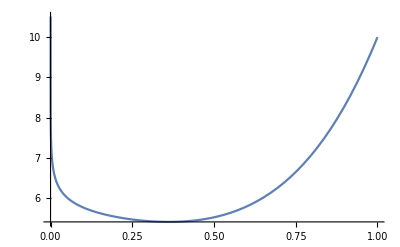

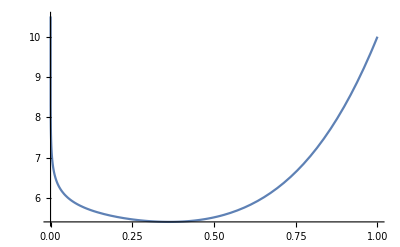

```mathematica
Plot[ϕAdSsol/.{C[1]->5,C[2]->5,m->0.5,l->1},{z,0,1}]
Plot[ϕAdSsolϵ/.{C[1]->5,C[2]->5,ϵ->1/16},{z,0,1}]
```

```mathematica
LbulkϵOnshell=FullSimplify[PowerExpand[Lbulkϵ/.{ϕ[z]->ϕAdSsolϵ,ϕ'[z]->D[ϕAdSsolϵ,z]}/.m->(√((ϵ+2)^2-4))/l]]
```

-2 l^3 z^(-5-2 ϵ) (2+ϵ) (z^(8+4 ϵ) (4+ϵ) C[1]^2+ϵ C[2]^2)

```mathematica
Integrate[LbulkϵOnshell,z]
VbulkEff =Simplify[(%/.z->zIR )- (%/.z->zUV)]
```

-l^3 z^(-2 (2+ϵ)) (z^(8+4 ϵ) (4+ϵ) C[1]^2-ϵ C[2]^2)

-l^3 zIR^(-2 (2+ϵ)) zUV^(-2 (2+ϵ)) (zIR^(4+2 ϵ)-zUV^(4+2 ϵ)) (zIR^(4+2 ϵ) zUV^(4+2 ϵ) (4+ϵ) C[1]^2+ϵ C[2]^2)

Now add in the contributions from the branes

```mathematica
LIR = -√gz λIR (ϕ[z]^2-vIR^2)^2 DiracDelta[z-zIR]
LUV = -√gz λUV (ϕ[z]^2-vUV^2)^2 DiracDelta[z-zUV]
```

-√(l^10/z^10) λIR DiracDelta[z-zIR] (-vIR^2+ϕ[z]^2)^2

-√(l^10/z^10) λUV DiracDelta[z-zUV] (-vUV^2+ϕ[z]^2)^2

```mathematica
VIREff =Integrate[D[LIR,ϕ[z]],{z,zIR-δ,zIR+δ},Assumptions->{zIR>0,δ>0}]
VUVEff=Integrate[D[LUV,ϕ[z]],{z,zUV-δ,zUV+δ},Assumptions->{zUV>0,δ>0}]
```

(4 √(l^10) λIR ϕ[zIR] (vIR^2-ϕ[zIR]^2))/zIR^5

(4 √(l^10) λUV ϕ[zUV] (vUV^2-ϕ[zUV]^2))/zUV^5

```mathematica
VTotalEff = VbulkEff +VIREff + VUVEff
```

-l^3 zIR^(-2 (2+ϵ)) zUV^(-2 (2+ϵ)) (zIR^(4+2 ϵ)-zUV^(4+2 ϵ)) (zIR^(4+2 ϵ) zUV^(4+2 ϵ) (4+ϵ) C[1]^2+ϵ C[2]^2)+(4 √(l^10) λIR ϕ[zIR] (vIR^2-ϕ[zIR]^2))/zIR^5+(4 √(l^10) λUV ϕ[zUV] (vUV^2-ϕ[zUV]^2))/zUV^5

In large λ limit we get

```mathematica
{vIR == ϕAdSsolϵ/.z->zIR,vUV== ϕAdSsolϵ/.z->zUV}
```

{vIR==zIR^-ϵ (zIR^(2 (2+ϵ)) C[1]+C[2]),vUV==zUV^-ϵ (zUV^(2 (2+ϵ)) C[1]+C[2])}

```mathematica
largeλbcsol=Solve[{vIR == ϕAdSsolϵ/.z->zIR,vUV== ϕAdSsolϵ/.z->zUV},{C[1],C[2]}]
```

{{C[1]→(vIR zIR^ϵ-vUV zUV^ϵ)/(zIR^(4+2 ϵ)-zUV^(4+2 ϵ)),C[2]→(zIR^ϵ zUV^ϵ (vUV zIR^(4+ϵ)-vIR zUV^(4+ϵ)))/(zIR^(4+2 ϵ)-zUV^(4+2 ϵ))}}

Expanding to second order in zUV/zIR we then get

```mathematica
largeλlargekrc ={C[1]->(vIR zIR^ϵ-vUV zUV^ϵ)1/zUV^(4+2 ϵ)(zUV^(4+2 ϵ)/zIR^(4+2 ϵ)+(zUV^(4+2 ϵ)/zIR^(4+2 ϵ))^2),C[2]->(vUV zIR^(4+ϵ)-vIR zUV^(4+ϵ))1/zUV^(4+2 ϵ)(zUV^(4+2 ϵ)/zIR^(4+2 ϵ)+(zUV^(4+2 ϵ)/zIR^(4+2 ϵ))^2)}
```

{C[1]→zUV^(-4-2 ϵ) (vIR zIR^ϵ-vUV zUV^ϵ) (zIR^(-4-2 ϵ) zUV^(4+2 ϵ)+zIR^(-8-4 ϵ) zUV^(8+4 ϵ)),C[2]→zUV^(-4-2 ϵ) (vUV zIR^(4+ϵ)-vIR zUV^(4+ϵ)) (zIR^(-4-2 ϵ) zUV^(4+2 ϵ)+zIR^(-8-4 ϵ) zUV^(8+4 ϵ))}

-l^3 zIR^(-2 (2+ϵ)) zUV^(-2 (2+ϵ)) (zIR^(4+2 ϵ)-zUV^(4+2 ϵ)) (zUV^(-8-4 ϵ) (vUV zIR^(4+ϵ)-vIR zUV^(4+ϵ))^2 (zIR^(-4-2 ϵ) zUV^(4+2 ϵ)+zIR^(-8-4 ϵ) zUV^(8+4 ϵ))^2 ϵ+zIR^(4+2 ϵ) zUV^(-4-2 ϵ) (vIR zIR^ϵ-vUV zUV^ϵ)^2 (zIR^(-4-2 ϵ) zUV^(4+2 ϵ)+zIR^(-8-4 ϵ) zUV^(8+4 ϵ))^2 (4+ϵ))

-vUV^2 zIR^(-10 (2+ϵ)) (-1+zIR^(4+2 ϵ)) (1+zIR^(4+2 ϵ))^2 ((1+a-zIR^(4+ϵ))^2 ϵ+zIR^(4+2 ϵ) (-1+(1+a) zIR^ϵ)^2 (4+ϵ))

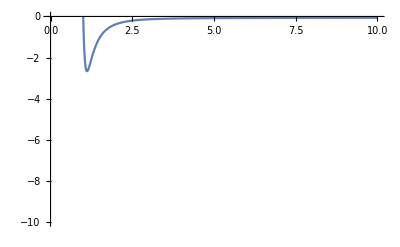

```mathematica
VbulkEff/.largeλlargekrc
Simplify[VbulkEff/.largeλlargekrc/.{zUV->1,l->1}/.vIR->vUV (1+a)]
Plot[1/vUV^2%/.{a->1,ϵ->0.1},{zIR,1,10},PlotRange->{-10,0}]
```

{-l^3 zIR^(-2 (2+ϵ)) zUV^(-2 (2+ϵ)) (zIR^(4+2 ϵ)-zUV^(4+2 ϵ)) ((zIR^(2 ϵ) zUV^(2 ϵ) (vUV zIR^(4+ϵ)-vIR zUV^(4+ϵ))^2 ϵ)/((zIR^(4+2 ϵ)-zUV^(4+2 ϵ))^2)+(zIR^(4+2 ϵ) zUV^(4+2 ϵ) (vIR zIR^ϵ-vUV zUV^ϵ)^2 (4+ϵ))/((zIR^(4+2 ϵ)-zUV^(4+2 ϵ))^2))}

{-(vUV^2 ((1+a-zIR^(4+ϵ))^2 ϵ+zIR^4 (-1+(1+a) zIR^ϵ)^2 (4+ϵ)))/(zIR^4 (-1+zIR^(4+2 ϵ)))}

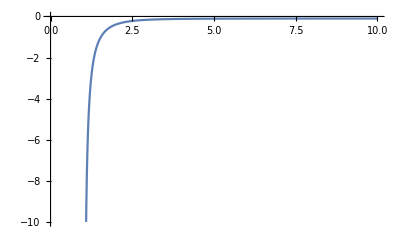

```mathematica
VbulkEff/.largeλbcsol
Simplify[VbulkEff/.largeλbcsol/.{zUV->1,l->1}/.vIR->vUV (1+a)]
Plot[1/vUV^2%/.{a->1,ϵ->0.1},{zIR,1,10},PlotRange->{-10,0}]
```

so WTF? it seems like we only have a minimum if we take the limit of large zUV/zIR, the limit is really supposed to be large krc which is limit of large brane separation compared to the ads radius so try decreasing the radius

{-(1.×10^-9 vUV^2 ((1+a-zIR^(4+ϵ))^2 ϵ+zIR^4 (-1+(1+a) zIR^ϵ)^2 (4+ϵ)))/(zIR^4 (-1+zIR^(4+2 ϵ)))}

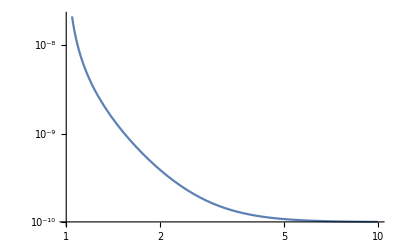

```mathematica
Simplify[VbulkEff/.largeλbcsol/.{zUV->1,l->0.001}/.vIR->vUV (1+a)]
LogLogPlot[-1/vUV^2%/.{a->1,ϵ->0.1},{zIR,1,10},PlotRange->{-10,0}]
```

-1.×10^-12 vUV^2 zIR^(-10 (2+ϵ)) (-1+zIR^(4+2 ϵ)) (1+zIR^(4+2 ϵ))^2 ((1+a-zIR^(4+ϵ))^2 ϵ+zIR^(4+2 ϵ) (-1+(1+a) zIR^ϵ)^2 (4+ϵ))

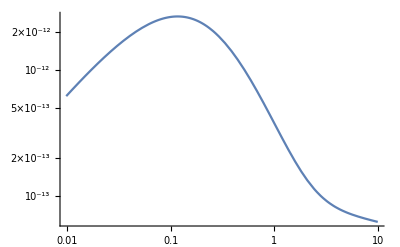

```mathematica
Simplify[VbulkEff/.largeλlargekrc/.{zUV->1,l->0.0001}/.vIR->vUV (1+a)]
LogLogPlot[-1/vUV^2%/.{a->1,ϵ->0.1}/.zIR->1+zSep,{zSep,0,10},PlotRange->{-10,0}]
```

From this it looks like a valid limit, so what gives???

#### In OG coordinates

Now we need the EOM of the scalar at the boundaries - here we switch to the original GW coordinates

```mathematica
σ[ϕ_] := k rc Abs[ϕ]
Φ[ϕ_] := E^(2 σ[ϕ])(A E^(σ[ϕ]ν)+B E^(-σ[ϕ]ν))
(- 1)/rc D[E^(-4 σ[ϕ])D[Φ[ϕ],ϕ],ϕ]+m^2 Φ[ϕ];
Simplify[%/.ϕ->0]
```

B (m^2-k (-2+ν) (k rc (2+ν) Abs'[0]^2-Abs''[0]))+A (m^2-k (2+ν) (k rc (-2+ν) Abs'[0]^2+Abs''[0]))

```mathematica
σnabs[ϕ_] := k rc ϕ
DSolve[1/rc^2 D[E^(-4 σnabs[ϕ])D[Φvar[ϕ],ϕ],ϕ]+m^2 E^(-4 σnabs[ϕ])Φvar[ϕ]==0,Φvar[ϕ],ϕ]
```

{{Φvar[ϕ]→ⅇ^((2 k rc-√(4 k^2 rc^2-m^2 rc^2)) ϕ) C[1]+ⅇ^((2 k rc+√(4 k^2 rc^2-m^2 rc^2)) ϕ) C[2]}}

```mathematica
σ[ϕ_] := k rc Abs[ϕ]
Φ[ϕ_] := E^(2 σ[ϕ])(A E^(σ[ϕ]ν)+B E^(-σ[ϕ]ν))
(- 1)/rc D[E^(-4 σ[ϕ])D[Φ[ϕ],ϕ],ϕ]+m^2 Φ[ϕ];
Simplify[%/.ϕ->π]
```

ⅇ^(-k π rc (2+ν)) (B (ⅇ^(4 k π rc) m^2-k (-2+ν) (k rc (2+ν) Abs'[π]^2-Abs''[π]))+A ⅇ^(2 k π rc ν) (ⅇ^(4 k π rc) m^2-k (2+ν) (k rc (-2+ν) Abs'[π]^2+Abs''[π])))

So this works, the Abs’’ give the delta functions which are used to match, but we can ignore this and just consider the limits that they use.

#### AdS - in OG coordinates

```mathematica
Clear[Φ]
σ[ϕ_] := k rc ϕ
gzE={{E^(-2 σ[ϕ]),0,0,0,0},{0,E^(-2 σ[ϕ]),0,0,0},{0,0,E^(-2 σ[ϕ]),0,0},{0,0,0,E^(-2 σ[ϕ]),0},{0,0,0,0,rc^2}};
gz = Det[gzE];

Lbulk = -√gz(Inverse[gzE][[5,5]] Φ'[ϕ]^2+m^2 Φ[ϕ]^2)
(*D[D[Lbulk,ϕ'[z]],z]==D[Lbulk,ϕ[z]]*)
Simplify[(D[D[Lbulk,Φ'[ϕ]],ϕ] )1/(√gz)]==Simplify[(D[Lbulk,Φ[ϕ]] )1/(√gz)]
ϕAdSsol = Φ[ϕ]/.Simplify[DSolve[%,Φ[ϕ],ϕ,Assumptions->{{l,m}∈Reals}]][[1,1]]
```

-√(ⅇ^(-8 k rc ϕ) rc^2) (m^2 Φ[ϕ]^2+Φ'[ϕ]^2/rc^2)

(8 k rc Φ'[ϕ]-2 Φ''[ϕ])/rc^2==-2 m^2 Φ[ϕ]

ⅇ^(2 k rc ϕ-√((4 k^2+m^2) rc^2) ϕ) (C[1]+ⅇ^(2 √((4 k^2+m^2) rc^2) ϕ) C[2])

ϵ = √(4+m^2 l^2)-2 so we can simplify the above expressions

```mathematica
ϕAdSsolϵ=Simplify[PowerExpand[Simplify[ϕAdSsol/.m->k √((ν)^2-4)]]]
Lbulkϵ=Lbulk/.m->k √((ν)^2-4)
```

ⅇ^(-k rc (-2+ν) ϕ) (C[1]+ⅇ^(2 k rc ν ϕ) C[2])

-√(ⅇ^(-8 k rc ϕ) rc^2) (k^2 (-4+ν^2) Φ[ϕ]^2+Φ'[ϕ]^2/rc^2)

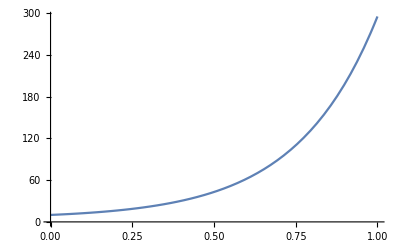

-Graphics-

```mathematica
Plot[ϕAdSsol/.{C[1]->5,C[2]->5,m->0.5,k->1,rc->1},{ϕ,0,1}]
Plot[ϕAdSsolϵ/.{C[1]->5,C[2]->5,ϵ->1/16,k->1,rc->0.1},{ϕ,0,1}]
```

```mathematica
(*LbulkϵOnshell=PowerExpand[FullSimplify[PowerExpand[Lbulkϵ/.{Φ[ϕ]->ϕAdSsolϵ,Φ'[ϕ]->D[ϕAdSsolϵ,z]}/.m->k √((ϵ+2)^2-4)]]]*)
LbulkϵOnshell=PowerExpand[FullSimplify[PowerExpand[Lbulkϵ/.{Φ[ϕ]->ϕAdSsolϵ,Φ'[ϕ]->D[ϕAdSsolϵ,ϕ]}/.m->k √((ν)^2-4)]]]/.ϵ->ν-2
```

-2 ⅇ^(-2 k rc ν ϕ) k^2 rc ν ((-2+ν) C[1]^2+ⅇ^(4 k rc ν ϕ) (2+ν) C[2]^2)

```mathematica
Integrate[LbulkϵOnshell,ϕ]
VbulkEff =FullSimplify[(%/.ϕ->π )- (%/.ϕ->0)]/.ϵ->ν-2
```

-ⅇ^(-2 k rc ν ϕ) k (-((-2+ν) C[1]^2)+ⅇ^(4 k rc ν ϕ) (2+ν) C[2]^2)

-ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k ((-2+ν) C[1]^2+ⅇ^(2 k π rc ν) (2+ν) C[2]^2)

In large λ limit we get

```mathematica
{vIR == ϕAdSsolϵ/.ϕ->π,vUV== ϕAdSsolϵ/.ϕ->0}
```

{vIR==ⅇ^(-k π rc (-2+ν)) (C[1]+ⅇ^(2 k π rc ν) C[2]),vUV==C[1]+C[2]}

```mathematica
ϕsolGW = E^(2 σ)(A E^(σ ν)+B E^(-σ ν))
largeλFullSol=Solve[{vIR == ϕsolGW/.σ->k rc π ,vUV== ϕsolGW /.σ->0},{A,B}]
ϕsolGW/.largeλFullSol[[1]]
Simplify[%/.σ-> k rc ϕ]
Simplify[%/.ϕ->0]
Simplify[%%/.ϕ-> π]
```

ⅇ^(2 σ) (B ⅇ^(-ν σ)+A ⅇ^(ν σ))

{{A→(ⅇ^(-2 k π rc) (ⅇ^(k π rc ν) vIR-ⅇ^(2 k π rc) vUV))/(-1+ⅇ^(2 k π rc ν)),B→(ⅇ^(-2 k π rc+k π rc ν) (-vIR+ⅇ^(2 k π rc+k π rc ν) vUV))/(-1+ⅇ^(2 k π rc ν))}}

ⅇ^(2 σ) ((ⅇ^(-2 k π rc+ν σ) (ⅇ^(k π rc ν) vIR-ⅇ^(2 k π rc) vUV))/(-1+ⅇ^(2 k π rc ν))+(ⅇ^(-2 k π rc+k π rc ν-ν σ) (-vIR+ⅇ^(2 k π rc+k π rc ν) vUV))/(-1+ⅇ^(2 k π rc ν)))

(ⅇ^(-k rc (2 π+(-2+ν) ϕ)) (-ⅇ^(k π rc ν) vIR+ⅇ^(k rc ν (π+2 ϕ)) vIR+ⅇ^(2 k π rc (1+ν)) vUV-ⅇ^(2 k rc (π+ν ϕ)) vUV))/(-1+ⅇ^(2 k π rc ν))

vUV

vIR

```mathematica
{vIR,vUV}==Simplify[{{ⅇ^(-k π rc (-2+ν)) ⅇ^(2 k π rc ν) ,ⅇ^(-k π rc (-2+ν))},{1,1}}.{A,B}]
```

{vIR,vUV}=={ⅇ^(-k π rc (-2+ν)) (B+A ⅇ^(2 k π rc ν)),A+B}

```mathematica
Simplify[Inverse[{{ⅇ^(-k π rc (-2+ν)) ⅇ^(2 k π rc ν) ,ⅇ^(-k π rc (-2+ν))},{1,1}}].{vIR,vUV}]
```

{(ⅇ^(k π rc (-2+ν)) vIR-vUV)/(-1+ⅇ^(2 k π rc ν)),(-ⅇ^(k π rc (-2+ν)) vIR+ⅇ^(2 k π rc ν) vUV)/(-1+ⅇ^(2 k π rc ν))}

```mathematica
Series[1/(a-1),{a,∞,2}]
```

1/a+(1/a)^2+O[1/a]^3

```mathematica
LargekrclimitFull = Expand[{A->(ⅇ^(k π rc (-2+ν)) vIR-vUV)(ⅇ^(-2 k π rc ν)+ⅇ^(-4 k π rc ν)) ,B->(-ⅇ^(k π rc (-2+ν)) vIR+ⅇ^(2 k π rc ν) vUV)(ⅇ^(-2 k π rc ν)+ⅇ^(-4 k π rc ν))}]
```

{A→ⅇ^(k π rc (-2+ν)-4 k π rc ν) vIR+ⅇ^(k π rc (-2+ν)-2 k π rc ν) vIR-ⅇ^(-4 k π rc ν) vUV-ⅇ^(-2 k π rc ν) vUV,B→-ⅇ^(k π rc (-2+ν)-4 k π rc ν) vIR-ⅇ^(k π rc (-2+ν)-2 k π rc ν) vIR+vUV+ⅇ^(-2 k π rc ν) vUV}

This is how they get their solution. The expand to second order in the exponential and

```mathematica
GWapprox={A->vIR E^(-(2+ν)k rc π)- vUV E^(-2ν k rc π),B-> vUV (1+E^(-2ν k rc π))-vIR E^(-(2+ν)k rc π)}
ϕsolGW = E^(2 σ)(A E^(σ ν)+B E^(-σ ν))/.GWapprox
Simplify[%/.σ->0]
Simplify[%%/.σ->k rc π]
```

{A→ⅇ^(k π rc (-2-ν)) vIR-ⅇ^(-2 k π rc ν) vUV,B→-ⅇ^(k π rc (-2-ν)) vIR+(1+ⅇ^(-2 k π rc ν)) vUV}

ⅇ^(2 σ) (ⅇ^(ν σ) (ⅇ^(k π rc (-2-ν)) vIR-ⅇ^(-2 k π rc ν) vUV)+ⅇ^(-ν σ) (-ⅇ^(k π rc (-2-ν)) vIR+(1+ⅇ^(-2 k π rc ν)) vUV))

vUV

vIR-ⅇ^(-2 k π rc ν) vIR+ⅇ^(k π rc (2-3 ν)) vUV

Which works since ν >= 2

-ⅇ^(-4 k π rc (1+2 ν)) (-1+ⅇ^(2 k π rc ν)) (1+ⅇ^(2 k π rc ν))^2 k (-4 ⅇ^(k π rc (2+ν)) vIR vUV ν+ⅇ^(4 k π rc) vUV^2 (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+vIR^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν)))

-ⅇ^(-4 k π rc (1+2 ν)) (-1+ⅇ^(2 k π rc ν)) (1+ⅇ^(2 k π rc ν))^2 k (-4 (1+a) ⅇ^(k π rc (2+ν)) ν+ⅇ^(4 k π rc) (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+(1+a)^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν)))

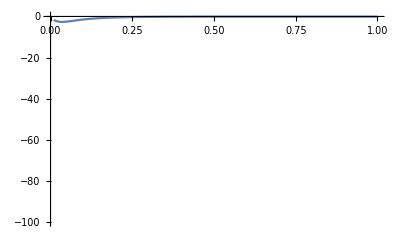

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ]
Simplify[1/vUV^2%/.vIR->vUV (1+a)]
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,1},PlotRange->{-100,0}]
```

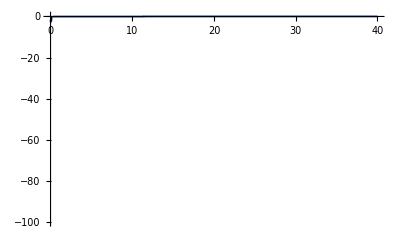

General::munfl: Exp[-1306.92] is too small to represent as a normalized machine number; precision may be lost.

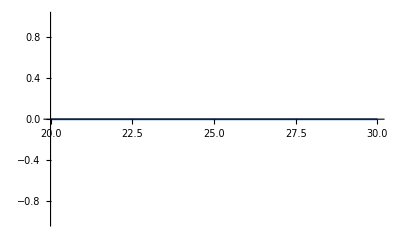

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40},PlotRange->{-100,0}]
Plot[%%/.{a->1,ν->2+0.1,k->1},{rc,20,30}]
```

```mathematica
N[4/π k^2/m^2 Log[1+a]/.{m->k  0.3,a->1}]
```

9.80603

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40},PlotRange->{-100,0}]
Plot[-%%/.{a->1,ν->√(4 + (0.3k)^2/k^2)}/.{k->1},{rc,5,10}]
```

-Graphics-

-Graphics-

check limit they consider explicitly with knowledge of where we expect it to be

```mathematica
N[4/π k^2/m^2 Log[1+a]/.{m->k  0.1,a->1}]
```

88.2542

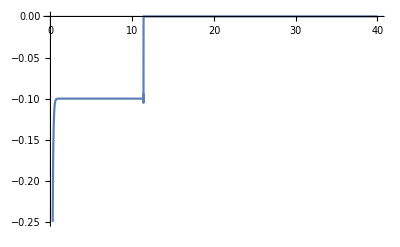

General::munfl: Exp[-5031.6] is too small to represent as a normalized machine number; precision may be lost.

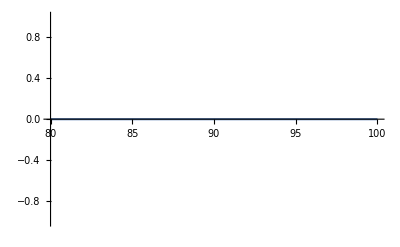

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40}]
Plot[-%%/.{a->1,ν->√(4 + (0.1k)^2/k^2)}/.{k->1},{rc,80,100}]
```

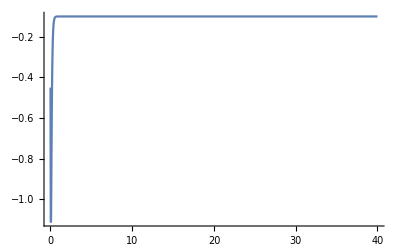

General::munfl: Exp[-1006.57] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1005.94] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.GWapprox ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40}]
Plot[-%%/.{a->1,ν->√(4 + (0.1k)^2/k^2)}/.{k->1},{rc,80,100}]
```

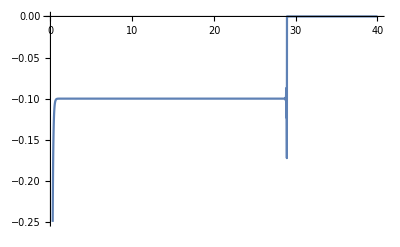

General::munfl: Exp[-1005.31] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.largeλFullSol[[1]] ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40}]
Plot[-%%/.{a->1,ν->√(4 + (0.1k)^2/k^2)}/.{k->1},{rc,80,100}]
```

```mathematica
N[Log[2]]
```

0.693147

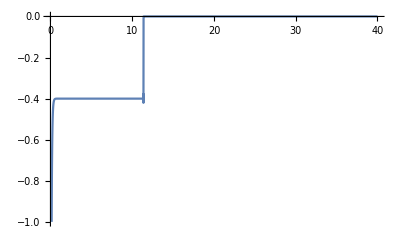

General::munfl: Exp[-1306.92] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ];
Simplify[1/vIR^2%/.vUV->vIR (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40}]
Plot[%%/.{a->1,ν->2+0.1,k->1},{rc,20,30}]
```

with 0.1 m^2/ k^2

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.GWapprox ];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,40}]
Plot[-%%/.{a->1,ν->√(4 + 0.1)}/.{k->1},{rc,80,100}]
```

-Graphics-

General::munfl: Exp[-1017.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1011.56] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

-(ⅇ^(-4 k π rc) k (-4 ⅇ^(k π rc (2+ν)) vIR vUV ν+ⅇ^(4 k π rc) vUV^2 (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+vIR^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν))))/(-1+ⅇ^(2 k π rc ν))

-(ⅇ^(-4 k π rc) k (-4 (1+a) ⅇ^(k π rc (2+ν)) ν+ⅇ^(4 k π rc) (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+(1+a)^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν))))/(-1+ⅇ^(2 k π rc ν))

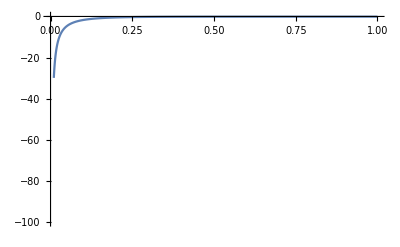

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.largeλFullSol[[1]]]
Simplify[1/vUV^2%/.vIR->vUV (1+a)]
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,1},PlotRange->{-100,0}]
```

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.largeλFullSol[[1]]]
Simplify[1/vUV^2%/.vIR->vUV (1+a)]
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,1},PlotRange->{-100,0}]
```

-(ⅇ^(-4 k π rc) k (-4 ⅇ^(k π rc (2+ν)) vIR vUV ν+ⅇ^(4 k π rc) vUV^2 (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+vIR^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν))))/(-1+ⅇ^(2 k π rc ν))

-(ⅇ^(-4 k π rc) k (-4 (1+a) ⅇ^(k π rc (2+ν)) ν+ⅇ^(4 k π rc) (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+(1+a)^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν))))/(-1+ⅇ^(2 k π rc ν))

-Graphics-

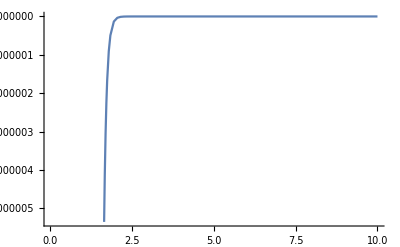

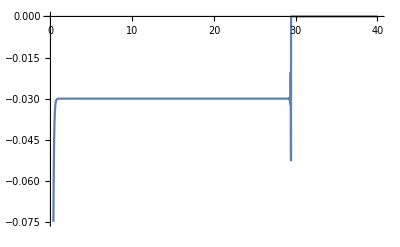

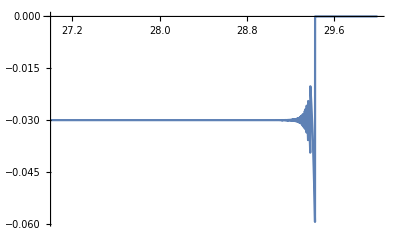

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.largeλFullSol[[1]]];
Simplify[1/vUV^2%/.vIR->vUV (1+a)];
Plot[%/.{a->1,ν->2+0.03,k->1},{rc,0.01,10}]
Plot[%%/.{a->1,ν->2+0.03,k->1},{rc,0.01,40}]
Plot[%%%/.{a->1,ν->2+0.03,k->1},{rc,27,30}]
```

-ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k ((-ⅇ^(-k π rc (2+ν)) vIR+vUV+ⅇ^(-2 k π rc ν) vUV)^2 (-2+ν)+ⅇ^(-2 k π rc ν) (-ⅇ^(k π rc (-2+ν)) vIR+vUV)^2 (2+ν))

-(ⅇ^(-2 k π rc ν) (-1+ⅇ^(2 k π rc ν)) k ((1+ⅇ^(-2 k π rc ν)-(1+a) ⅇ^(-k π rc (2+ν)))^2 vUV^2 (-2+ν)+ⅇ^(-2 k π rc ν) (vUV-(1+a) ⅇ^(k π rc (-2+ν)) vUV)^2 (2+ν)))/vUV^2

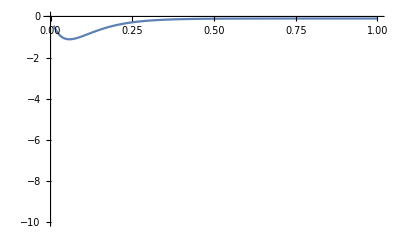

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.GWapprox]
Simplify[1/vUV^2(%/.vIR->vUV (1+a))]
Plot[%/.{a->1,ν->2+0.1,k->1},{rc,0.01,1},PlotRange->{-10,0}]
```

-ⅇ^(-4 k π rc (1+2 ν)) (-1+ⅇ^(2 k π rc ν)) (1+ⅇ^(2 k π rc ν))^2 k (-4 ⅇ^(k π rc (2+ν)) vIR vUV ν+ⅇ^(4 k π rc) vUV^2 (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+vIR^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν)))

-ⅇ^(-4 k π rc (1+2 ν)) (-1+ⅇ^(2 k π rc ν)) (1+ⅇ^(2 k π rc ν))^2 k (-4 (1+a) ⅇ^(k π rc (2+ν)) ν+ⅇ^(4 k π rc) (2+ⅇ^(2 k π rc ν) (-2+ν)+ν)+(1+a)^2 (-2+ν+ⅇ^(2 k π rc ν) (2+ν)))

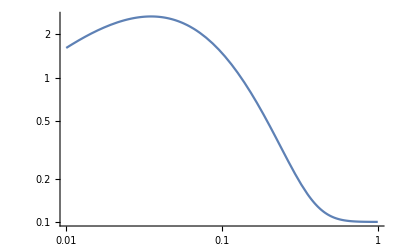

```mathematica
Simplify[VbulkEff/.{C[1]->B,C[2]->A}/.LargekrclimitFull ]
Simplify[1/vUV^2%/.vIR->vUV (1+a)]
LogLogPlot[-%/.{a->1,ν->2+0.1,k->1},{rc,0.01,1}]
```

krc is large here, so it seems like the limit is valid, I don’t understand why the other solution doesn’t work.

NO IT’S NOT. THIS IS gives small krc

Also check if delta function condition works or not

```mathematica
largeλbfromδs=Solve[{0==((2+ν)A + (2-ν)B) ,0==((2+ν)E^(ν k rc π)A + (2-ν)E^(-ν k rc π)B)},{A,B}]
ϕsolGW/.largeλbfromδs[[1]]
Simplify[%/.σ-> k rc ϕ]
Simplify[%/.ϕ->0]
Simplify[%%/.ϕ-> π]
```

{{A→0,B→0}}

ⅇ^(2 σ) (ⅇ^(ν σ) (ⅇ^(k π rc (-2-ν)) vIR-ⅇ^(-2 k π rc ν) vUV)+ⅇ^(-ν σ) (-ⅇ^(k π rc (-2-ν)) vIR+(1+ⅇ^(-2 k π rc ν)) vUV))

ⅇ^(-k rc (2 π ν+(-2+ν) ϕ)) (-ⅇ^(k π rc (-2+ν)) vIR+ⅇ^(k rc (π (-2+ν)+2 ν ϕ)) vIR+vUV+ⅇ^(2 k π rc ν) vUV-ⅇ^(2 k rc ν ϕ) vUV)

vUV

vIR-ⅇ^(-2 k π rc ν) vIR+ⅇ^(k π rc (2-3 ν)) vUV

#### ρ GW AdS

```mathematica
gρE=ρ^2/l^2{{1,0,0,0,0},{0,(ρ^2/l^2)^-2,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
gρ = Det[gρE];

Lbulk = -√gρ(Inverse[gρE][[2,2]] ϕ'[ρ]^2+m^2 ϕ[ρ]^2)
(*D[D[Lbulk,ϕ'[z]],z]==D[Lbulk,ϕ[z]]*)
Simplify[(D[D[Lbulk,ϕ'[ρ]],ρ] )l^2/(√gρ)]==Simplify[(D[Lbulk,ϕ[ρ]] )l^2/(√gρ)]
ϕAdSsol = ϕ[ρ]/.Simplify[DSolve[%,ϕ[ρ],ρ,Assumptions->{{l,m}∈Reals}]][[1,1]]
```

-√(ρ^6/l^6) (m^2 ϕ[ρ]^2+(ρ^2 ϕ'[ρ]^2)/l^2)

-2 ρ (5 ϕ'[ρ]+ρ ϕ''[ρ])==-2 l^2 m^2 ϕ[ρ]

ρ^(-2-√(4+l^2 m^2)) (ρ^(2 √(4+l^2 m^2)) C[1]+C[2])

#### GW from CR

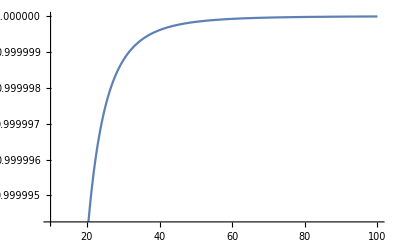

```mathematica
Plot[1-z^-4,{z,10,100}]
```

#### Series expand for large y (far from horizon)

```mathematica
Clear[ϵ]
Solve[ϵ== (-2+√(4+l^2 m^2)),m]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{m→-(√ϵ √(4+ϵ))/l},{m→(√ϵ √(4+ϵ))/l}}

```mathematica
ϕos1type3 = PowerExpand[Simplify[LegendreP[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]
ϕos2type3 =PowerExpand[Simplify[LegendreQ[1/4 (-2+√(4+l^2 m^2)),0,3,-1+2 y]/.m->(√(ϵ(4+ϵ)))/l]]
```

LegendreP[ϵ/4,-1+2 y]

LegendreQ[ϵ/4,0,3,-1+2 y]

```mathematica
Normal[Series[ϕos1type3,{y,∞,1}]]
Psol =FullSimplify[%/.y->hd+1]
```

(-2+2 y)^(ϵ/4) ((2^(-ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2+(2^(-3-ϵ/4) ϵ Gamma[1+ϵ/2])/(y Gamma[1+ϵ/4]^2))+(-2+2 y)^(-1-ϵ/4) ((2^(1+ϵ/4) Gamma[-1-ϵ/2])/Gamma[-ϵ/4]^2-(2^(-2+ϵ/4) (4+ϵ) Gamma[-1-ϵ/2])/(y Gamma[-ϵ/4]^2))

(hd^(-ϵ/4) (((4+8 hd-ϵ) Gamma[-1-ϵ/2])/(hd Gamma[-ϵ/4]^2)+(hd^(ϵ/2) (8+8 hd+ϵ) Gamma[1+ϵ/2])/Gamma[(4+ϵ)/4]^2))/(8 (1+hd))

```mathematica
Normal[Series[ϕos1type3/.y->hd+1,{hd,∞,1}]]
Series[FullSimplify[%],{ϵ,0,1}]
Normal[%]
```

(-2+2 (1+hd))^(-ϵ/4) ((-2+2 (1+hd))^(ϵ/2) ((2^(-ϵ/4) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2+(2^(-3-ϵ/4) ϵ Gamma[1+ϵ/2])/(hd Gamma[1+ϵ/4]^2))+(2^(ϵ/4) Gamma[-1-ϵ/2])/(hd Gamma[-ϵ/4]^2))

1+((1+hd Log[hd]) ϵ)/(4 hd)+O[ϵ]^2

1+(ϵ (1+hd Log[hd]))/(4 hd)

```mathematica
Normal[Series[ϕos2type3/.y->hd+1,{hd,∞,1}]]
Series[FullSimplify[%],{ϵ,0,1}]
Normal[%]
```

(2^(-2-ϵ/2) hd^(-1-ϵ/4) √π Gamma[1+ϵ/4])/Gamma[3/2+ϵ/4]

1/(2 hd)+((-EulerGamma-2 Log[2]-Log[hd]-PolyGamma[0,3/2]) ϵ)/(8 hd)+O[ϵ]^2

1/(2 hd)+(ϵ (-EulerGamma-2 Log[2]-Log[hd]-PolyGamma[0,3/2]))/(8 hd)

```mathematica
Normal[Series[ϕos2type3,{y,∞,1}]]
Qsol = Simplify[%/.y->hd+1]
```

(2^(-2-ϵ/2) √π y^(-1-ϵ/4) Gamma[1+ϵ/4])/Gamma[3/2+ϵ/4]

(2^(-2-ϵ/2) (1+hd)^(-1-ϵ/4) √π Gamma[1+ϵ/4])/Gamma[(6+ϵ)/4]

```mathematica
Simplify[A Psol + B Qsol]
```

((A hd^(ϵ/4) (8+8 hd+ϵ) Gamma[1+ϵ/2])/Gamma[1+ϵ/4]^2+(A hd^(-1-ϵ/4) (4+8 hd-ϵ) Gamma[-1-ϵ/2])/Gamma[-ϵ/4]^2+(2^(1-ϵ/2) B (1+hd)^(-ϵ/4) √π Gamma[1+ϵ/4])/Gamma[(6+ϵ)/4])/(8 (1+hd))

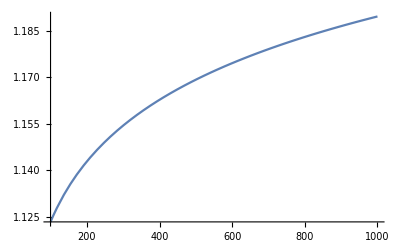

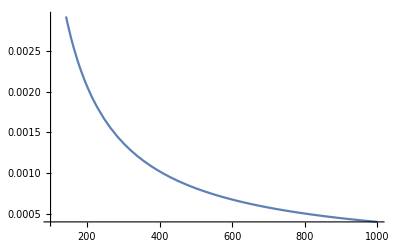

```mathematica
Plot[Psol/.ϵ->1/10,{hd,100,1000}]
Plot[Qsol/.ϵ->1/10,{hd,100,1000}]
```

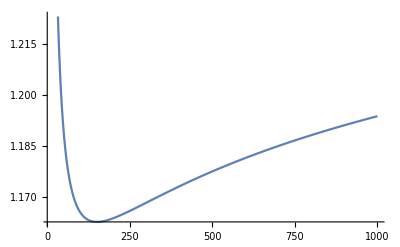

```mathematica
Plot[10Qsol+Psol/.ϵ->1/10,{hd,10,1000}]
```

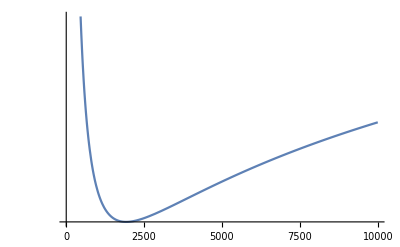

```mathematica
LogPlot[10ϕos2type3+ϕos1type3/.{ϵ->1/100,y->hd +1},{hd,0,10000}]
```

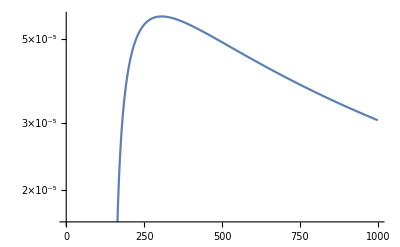

```mathematica
LogPlot[(10ϕos2type3+ϕos1type3)D[(10ϕos2type3+ϕos1type3),y]/.{ϵ->1/10,y->hd +1},{hd,0,1000}]
```

#### Find effective potential in terms of y

```mathematica
gzE=l^2/z^2{{g[z],0,0,0,0},{0,1/g[z],0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}};
X= {t,zh/y^(1/4),x1,x2,x3};
x= {t,y,x1,x2,x3};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,5}];
gyE= Simplify[Transpose[JXx].(gzE/.g[z]->1-z^4/zh^4/.z->zh/y^(1/4)).JXx ];
gyE //MatrixForm 
g5y = Simplify[Det[gy]]
```

((l^2 (-1+y))/(√y zh^2) | 0 | 0 | 0 | 0
0 | l^2/(16 (-1+y) y) | 0 | 0 | 0
0 | 0 | (l^2 √y)/zh^2 | 0 | 0
0 | 0 | 0 | (l^2 √y)/zh^2 | 0
0 | 0 | 0 | 0 | (l^2 √y)/zh^2)

l^10/(16 zh^8)

```mathematica
N[(Inverse[gyE][[2,2]] D[(10ϕos2type3+ϕos1type3),y]^2+m^2 (10ϕos2type3+ϕos1type3)^2)/.{ϵ->1/10,y->hd +1,m->1/10}]/.hd->1
```

(0.183583+0. ⅈ)+(184.58+0. ⅈ)/l^2

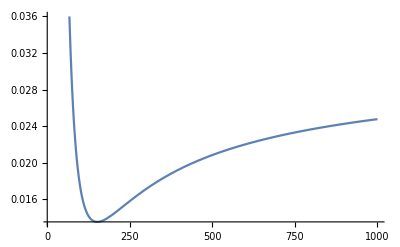

```mathematica
Plot[(Inverse[gyE][[2,2]] D[(10ϕos2type3+ϕos1type3),y]^2+m^2 (10ϕos2type3+ϕos1type3)^2)/.{ϵ->1/10,y->hd +1,m->1/10,l->1},{hd,10,1000}]
```

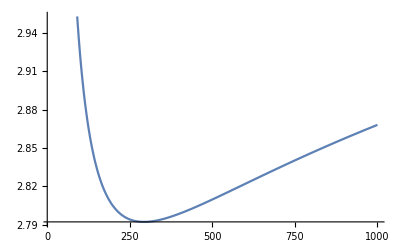

```mathematica
Plot[(Inverse[gyE][[2,2]] D[(-10ϕos2type3+10ϕos1type3),y]^2+m^2 (-10ϕos2type3+10ϕos1type3)^2)/.{ϵ->1/10,y->hd +1,m->1/10,l->1},{hd,10,1000}]
```

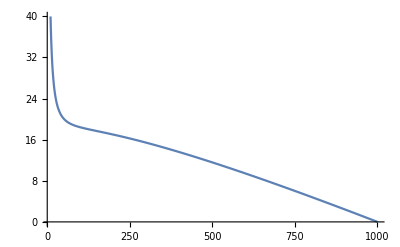

```mathematica
Plot[NIntegrate[(Inverse[gyE][[2,2]] D[(10ϕos2type3+ϕos1type3),y]^2+m^2 (10ϕos2type3+ϕos1type3)^2)/.{ϵ->1/10,m->1/10,l->1,y->hdp +1},{hdp,hd,1000}],{hd,10,1000}]
```

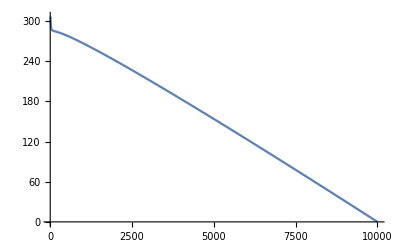

```mathematica
Plot[NIntegrate[(Inverse[gyE][[2,2]] D[(10ϕos2type3+ϕos1type3),y]^2+m^2 (10ϕos2type3+ϕos1type3)^2)/.{ϵ->1/10,m->1/10,l->1,y->hdp +1},{hdp,hd,10000}],{hd,10,10000}]
```

#### Evaluate effective potential in large y expansion

```mathematica
Normal[Series[ϕos1type3/.y->hd+1,{hd,∞,1}]];
Series[FullSimplify[%],{ϵ,0,1}];
PsolLargey = Normal[%]

Normal[Series[ϕos2type3/.y->hd+1,{hd,∞,1}]];
Series[FullSimplify[%],{ϵ,0,1}];
QsolLargey = Normal[%]
```

1+(ϵ (1+hd Log[hd]))/(4 hd)

1/(2 hd)+(ϵ (-EulerGamma-2 Log[2]-Log[hd]-PolyGamma[0,3/2]))/(8 hd)

```mathematica
ϕsolLargey = Simplify[A PsolLargey + B QsolLargey]
ϕsolLargeytruncd = - (-2 A (4 hd+ϵ)+(B-2 A hd) ϵ Log[hd])/(8 hd)
```

-(-2 A (4 hd+ϵ)+(B-2 A hd) ϵ Log[hd]+B (-4+EulerGamma ϵ+ϵ (Log[4]+PolyGamma[0,3/2])))/(8 hd)

-(-2 A (4 hd+ϵ)+(B-2 A hd) ϵ Log[hd])/(8 hd)

```mathematica
hdpot = FullSimplify[Integrate[((gyE[[2,2]]/.y->hd+1/.l->1)D[ϕsolLargeytruncd,hd]^2+m^2 ϕsolLargeytruncd^2 /.ϵ->(-2+√(4+ m^2)))/.m->1/10,hd]]
```

-1/(2211840000 hd^4)((-801+40 √401) B^2 (-3375+8 hd (500+27 hd (-25+68 hd))+12 Log[hd] (675+4 hd (-200+9 hd (25+2 hd (-8+25 hd)))+6 Log[hd] (-75+2 hd (50-3 hd (25-42 hd+50 hd^2))+100 hd^4 Log[hd]))-21600 hd^4 (-1+Log[hd])^2 Log[1+hd])+864 A^2 (25 (801-40 √401)+4 hd (25 (-801+40 √401)+50 (801-40 √401) hd+96 (-801+40 √401) hd^2+8 (-2401+80 √401) hd^4)+16 hd^4 (Log[hd] (-18425+920 √401+(3202-160 √401) hd+(-801+40 √401) (1+hd) Log[hd])+25 (801-40 √401) Log[1+hd]))-24 A B (720 (-3685+184 √401) hd^4 Log[hd]^2+192 (-801+40 √401) hd^4 Log[hd]^3-12 (-801+40 √401) Log[hd] (75+4 hd (-50+3 hd (25-46 hd+50 hd^2))+600 hd^4 Log[1+hd])+(-801+40 √401) (675-8 hd (200+9 hd (-25+8 hd))+7200 hd^4 Log[1+hd]))+43200 (-801+40 √401) B hd^4 ((4 A+B-B Log[hd]) PolyLog[2,-hd]+B PolyLog[3,-hd]))

```mathematica
Series[hdpot,{hd,∞,-1}]
Series[hdpot,{hd,∞,0}]
```

-((A^2 (-4802+160 √401+3202 Log[hd]-160 √401 Log[hd]-801 Log[hd]^2+40 √401 Log[hd]^2)) hd)/160000+O[1/hd]^0

-((A^2 (-4802+160 √401+3202 Log[hd]-160 √401 Log[hd]-801 Log[hd]^2+40 √401 Log[hd]^2)) hd)/160000+1/7680000(-80100 A B π^2+4000 √401 A B π^2-20025 B^2 π^2+1000 √401 B^2 π^2-76800 A^2 Log[hd]+3840 √401 A^2 Log[hd]+38448 A^2 Log[hd]^2-1920 √401 A^2 Log[hd]^2+19200 A B Log[hd]^2-960 √401 A B Log[hd]^2-12816 A B Log[hd]^3+640 √401 A B Log[hd]^3)+O[1/hd]^1

```mathematica
(gyE[[2,2]]/.y->hd+1/.l->1)D[ϕsolLargeytruncd,hd]^2+m^2 ϕsolLargeytruncd^2 /.m->(√(ϵ(ϵ+4)))
hdpotm = FullSimplify[Integrate[((gyE[[2,2]]/.y->hd+1/.l->1)D[ϕsolLargeytruncd,hd]^2+m^2 ϕsolLargeytruncd^2 /.m->(√(ϵ(ϵ+4)))),hd]]
```

(ϵ (4+ϵ) (-2 A (4 hd+ϵ)+(B-2 A hd) ϵ Log[hd])^2)/(64 hd^2)+((-(-8 A+((B-2 A hd) ϵ)/hd-2 A ϵ Log[hd])/(8 hd)+(-2 A (4 hd+ϵ)+(B-2 A hd) ϵ Log[hd])/(8 hd^2))^2)/(16 hd (1+hd))

1/(884736 hd^4)ϵ (864 A^2 (-ϵ+4 hd (ϵ-2 hd ϵ+32 hd^4 (32-8 ϵ+ϵ^3)-4 hd^2 ϵ (-1+4 ϵ (4+ϵ))))+24 A B ϵ (-27+8 hd (8+9 hd (-1+32 hd ϵ (4+ϵ))))-B^2 ϵ (135+8 hd (-20+27 hd (1+4 hd (-1+32 ϵ (4+ϵ)))))+12 ϵ (24 B hd^4 (B-64 A ϵ (4+ϵ)) Log[hd]^3-72 (4 A+B)^2 hd^4 Log[1+hd]-6 Log[hd]^2 (-768 A^2 hd^4 (1+hd) ϵ (4+ϵ)+48 A B hd^4 (129+32 ϵ)+B^2 (3+2 hd (-2+3 hd (1+2 hd (-1+hd+16 ϵ (4+ϵ)))))+12 B^2 hd^4 Log[1+hd])+Log[hd] (-1152 A^2 hd^4 (-129-32 ϵ+8 hd (-16+ϵ^2))+B^2 (27+4 hd (-8+9 hd (1+2 hd (hd-32 ϵ (4+ϵ)))))+24 A B (3+4 hd (-2+3 hd (1+2 hd (-1+hd+8 ϵ (4+ϵ)))))+144 B (4 A+B) hd^4 Log[1+hd]))+1728 B hd^4 ϵ ((4 A+B-B Log[hd]) PolyLog[2,-hd]+B PolyLog[3,-hd]))

```mathematica
Series[hdpotm,{hd,∞,-1}]
Series[hdpotm,{hd,∞,0}]
```

1/16 A^2 ϵ (4+ϵ) (16-8 ϵ+2 ϵ^2+8 ϵ Log[hd]-2 ϵ^2 Log[hd]+ϵ^2 Log[hd]^2) hd+O[1/hd]^0

1/16 A^2 ϵ (4+ϵ) (16-8 ϵ+2 ϵ^2+8 ϵ Log[hd]-2 ϵ^2 Log[hd]+ϵ^2 Log[hd]^2) hd+1/3072 ϵ^2 (-4 A B π^2-B^2 π^2+6144 A^2 Log[hd]+1536 A^2 ϵ Log[hd]-1536 A B Log[hd]^2+768 A^2 ϵ Log[hd]^2-384 A B ϵ Log[hd]^2+192 A^2 ϵ^2 Log[hd]^2-256 A B ϵ Log[hd]^3-64 A B ϵ^2 Log[hd]^3)+O[1/hd]^1

```mathematica
hdpotmder=Normal[Series[D[hdpotm,hd],{hd,∞,1}]]
Bsoln = Solve[%==0,{B}]
```

1/16 (64 A^2 ϵ+16 A^2 ϵ^2+32 A^2 ϵ^2 Log[hd]+8 A^2 ϵ^3 Log[hd]+4 A^2 ϵ^3 Log[hd]^2+A^2 ϵ^4 Log[hd]^2)+(32 A^2 ϵ^2+8 A^2 ϵ^3-16 A B ϵ^2 Log[hd]+8 A^2 ϵ^3 Log[hd]-4 A B ϵ^3 Log[hd]+2 A^2 ϵ^4 Log[hd]-4 A B ϵ^3 Log[hd]^2-A B ϵ^4 Log[hd]^2)/(16 hd)

{{B→(A (4 hd+2 ϵ+hd ϵ Log[hd]))/(ϵ Log[hd])}}

```mathematica
Simplify[D[hdpotmder,hd]/.Bsoln[[1]]]
```

(A^2 ϵ (4+ϵ) (4+ϵ Log[hd]) (-2 (2 hd+ϵ)+4 hd Log[hd]+hd ϵ Log[hd]^2))/(16 hd^2 Log[hd])

THis looks like it’s generically postivie, which means this is a minimum!